# Mathematica Notebook for “Background: Physics and Math of Shading”

This notebook contains some computations referenced in the course notes.

```mathematica
Off[NIntegrate::inumr]
SetOptions[Plot,PlotRange->All];

(* Based on the Solarized color scheme: http://ethanschoonover.com/solarized *)
pCol=Hue[0,0.79,0.86]; 
bCol=Hue[0.57,0.82,0.82];
tsCol=Hue[0.1];
trCol=Hue[0.19,1,0.6];
abcCol=Hue[0.66,0.45,0.77];
sgdCol=Hue[0.125,1,0.71];
```

## Phong NDF

This is the unnormalized Phong distribution function:

```mathematica
unnormalizedphong=Cos[θ]^αp;
```

Compute the normalization factor (relative to projected area) for the Phong distribution function:

```mathematica
phongnormf=Integrate[unnormalizedphong Sin[θ]Cos[θ],{ϕ,-π,π},{θ,0,π/2},Assumptions->{αp>0}]
```

(2 π)/(2+αp)

```mathematica
phong=unnormalizedphong/phongnormf
```

((2+αp) Cos[θ]^αp)/(2 π)

Here are the distribution curves for some logarithmically spaced cosine powers (as well as 0, which corresponds to the uniform distribution):

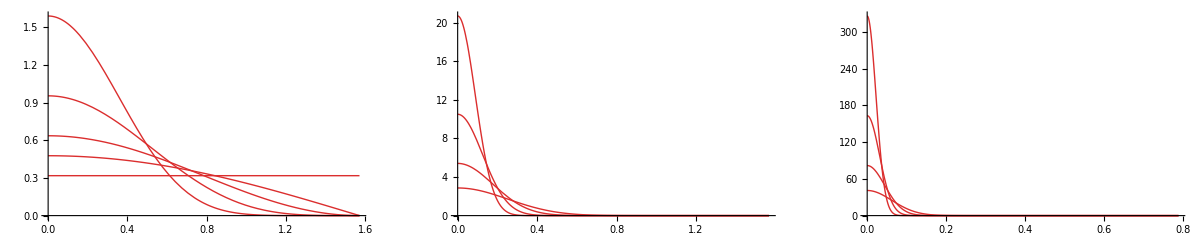

```mathematica
GraphicsRow[{Plot[phong/.αp->#&/@{0,1,2,4,8},{θ,0,π/2},PlotStyle->pCol],Plot[phong/.αp->#&/@{16,32,64,128},{θ,0,π/2},PlotStyle->pCol],Plot[phong/.αp->#&/@{256,512,1024,2048},{θ,0,π/2},PlotStyle->pCol]}, ImageSize->Full]
```

And an interactive graph:

```mathematica
Manipulate[Plot[phong/.αp->(8000^a-1),{θ,0,π/2},PlotStyle->pCol],{{a,0.25},0,1}]
```

## Beckmann NDF

This is the unnormalized Beckmann distribution function:

```mathematica
unnormalizedbeckmann=1/(αb^2 Cos[θ]^4)ⅇ^(-((1-Cos[θ]^2)/(Cos[θ]^2 αb^2)));
```

Compute the normalization factor (relative to projected area) for the Beckmann distribution function:

```mathematica
beckmannnormf=Integrate[unnormalizedbeckmann Sin[θ]Cos[θ],{ϕ,-π,π},{θ,0,π/2},Assumptions->{αb>0}]
```

π

We see here that the correct normalization factor for the Beckmann distribution, given normalization over projected area, is 1/π.

```mathematica
beckmann=unnormalizedbeckmann/beckmannnormf
```

(ⅇ^(-((1-Cos[θ]^2) Sec[θ]^2)/αb^2) Sec[θ]^4)/(π αb^2)

The Beckmann α_b parameter is equal to the RMS (root mean square) microfacet slope. Therefore its valid range is from 0 (non-inclusive – 0 corresponds to a perfect mirror or Dirac delta and causes divide by 0 errors in the Beckmann formulation) and up to arbitrarily high values. There is no special significance to a value of 1 – this just means that the RMS slope is 1/1 or 45°. We will look at the shape of the Beckmann NDF for moderately rough surfaces (m from 0.4 to 1):

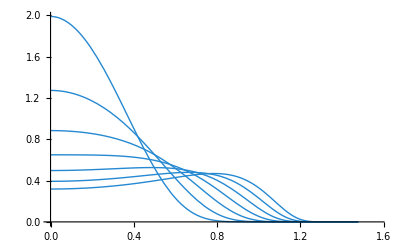

```mathematica
Plot[beckmann/.αb->#&/@Range[0.4,1.0,0.1],{θ,0,π/2},PlotStyle-> bCol]
```

We see here that at α_bvalues above 0.75, a local minimum starts appearing at 0°. This is significantly different than a Phong or Gaussian lobe, where the "roughest" possible surface is a uniform distribution. The Beckmann distribution is qualitatively different in that its parameter is not related to the variance of the angle but the mean of the slope. Thus a "very rough" surface in the Beckmann context is not a uniform or almost-uniform distribution, but a distribution clustered around high slopes. Let us look at even larger values of m:

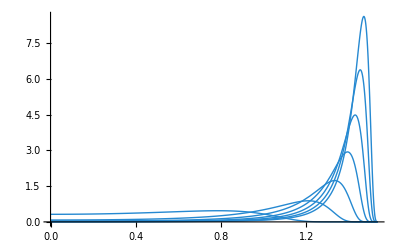

```mathematica
Plot[beckmann/.αb->#&/@Range[1,7],{θ,0,π/2},PlotStyle->bCol]
```

This behavior is unfortunate for environment map prefiltering, since the frequency content of the NDF decreases to a certain roughness and then starts increasing with m, Beckmann is supposed to be a good match to real-world measurements, but I am not sure over what range of parameters these comparisons were carried out. Are values this high (or even higher than 0.75, where the local minima starts appearing) observed in practice?

Let us compare the Beckmann and Phong NDF, using an equivalence between the parameters of the two NDFs published in "Microfacet Models for Refraction through Rough Surfaces" (EGSR 2007) - note that the equivalence breaks down for α_b>1:

```mathematica
αb2αp[αb_]:=  2/αb^2-2
```

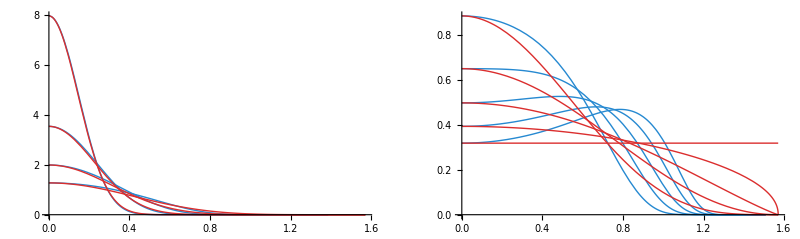

```mathematica
GraphicsRow[{Plot[{beckmann/.αb->#&/@Range[0.2,0.5,0.1],phong/.αp->αb2αp[#]&/@Range[0.2,0.5,0.1]},    {θ,0,π/2},PlotStyle->{bCol,pCol}],Plot[{beckmann/.αb->#&/@Range[0.6,1.0,0.1],phong/.αp->αb2αp[#]&/@Range[0.6,1.0,0.1]},    {θ,0,π/2},PlotStyle->{bCol,pCol}]},ImageSize->Full]
```

For rough surfaces (left plot), the equivalence holds about as well as can be expected, but the shape of the NDFs starts to differ significantly as m increases. For relatively smooth surfaces (right plot) the two NDFs match surprisingly well. This is to Phong’s credit, who devised his NDF (although not as such) purely from observation. As the value of α_b decreases, the match improves.

Interactive graph for “normal” (not super-rough) values, comparing with Phong:

```mathematica
Manipulate[Plot[{beckmann/.αb->a,phong/.αp->αb2αp[a]},{θ,0,π/2},PlotStyle->{bCol,pCol}],{{a,0.25},0.01,1.0}]
```

Interactive graph for Beckmann by itself for super-rough values:

```mathematica
Manipulate[Plot[beckmann/.αb->a,{θ,0,π/2},PlotStyle->bCol],{a,1.0,10.0}]
```

## Torrance-Sparrow NDF

This NDF is a Gaussian on the angle between the microfacet normal and the macroscopic surface normal. We will need to normalize it since Torrance and Sparrow did not supply a normalization factor:

```mathematica
unnormalizedtorrancesparrow=ⅇ^(-(θ/αts)^2);
```

We'll try for an analytical normalization factor:

```mathematica
normts=Integrate[unnormalizedtorrancesparrow Sin[θ]Cos[θ],{ϕ,-π,π},{θ,0,π/2},Assumptions->{αts>0}]
```

1/4 ⅇ^(-αts^2) π^(3/2) αts (-ⅈ Erf[π/(2 αts)-ⅈ αts]+ⅈ Erf[π/(2 αts)+ⅈ αts]+2 Erfi[αts])

Wow, that’s ugly! It also appears to be complex-valued, which is odd since the function being integrated was real-valued. Let’s see if it is really complex-valued:

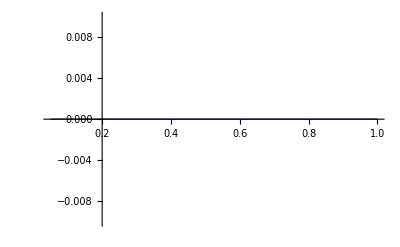

```mathematica
Plot[Im[normts],{αts,0.05,1},{PlotRange->{-0.01,0.01},PlotStyle->Thick}]
```

The imaginary part is 0 – looks like the normalization factor actually is real-valued and Mathematica is just being weird. If we were actually going to use this, we would fit a cheap function to the curve instead of using the analytical expression. But since we are just comparing it to other NDFs, no need to do that.  Let’s compare it to Blinn-Phong, using the Beckmann parameter conversion (according to the Cook-Torrance paper, the Beckmann and Torrance-Sparrow parameterizations are the same – both are equal to RMS slope):

```mathematica
torrancesparrow=unnormalizedtorrancesparrow/Re[normts]
```

(4 ⅇ^(-θ^2/αts^2))/(π^(3/2) Re[ⅇ^(-αts^2) αts (-ⅈ Erf[π/(2 αts)-ⅈ αts]+ⅈ Erf[π/(2 αts)+ⅈ αts]+2 Erfi[αts])])

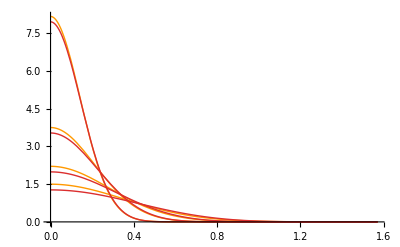

```mathematica
Plot[{torrancesparrow/.αts->#&/@Range[0.2,0.5,0.1],phong/.αp->αb2αp[#]&/@Range[0.2,0.5,0.1]},{θ,0,π/2},PlotStyle->{tsCol,pCol}]
```

The curves do look similar, but it appears that the equivalence between the parameterizations of the two distributions is a bit different than the one implied in the Cook-Torrance paper. We could work out the exact equivalence, but if the Torrance-Sparrow NDF turns out to have similar behavior to Phong over the whole range then it would be wasted effort since there would be no reason to use the (much more expensive) Torrance-Sparrow NDF. Let’s adjust parameter values manually to make the peaks coincide:

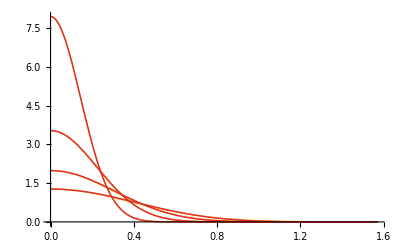

```mathematica
Plot[{torrancesparrow/.αts->#&/@{0.2027,0.3097,0.425,0.552},phong/.αp->αb2αp[#]&/@Range[0.2,0.5,0.1]},{θ,0,π/2},PlotStyle->{{tsCol,Thick},pCol}]
```

The curves appear to be extremely close. Let’s look at a rougher part of the domain:

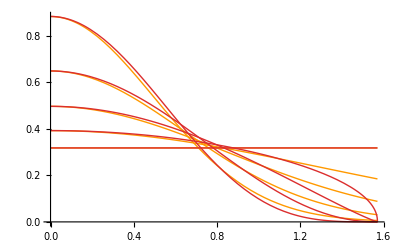

```mathematica
Plot[{torrancesparrow/.αts->#&/@{0.7035,0.899,1.195,1.81},torrancesparrow/.αts->100.0,phong/.αp->αb2αp[#]&/@Range[0.6,1.0,0.1]},{θ,0,π/2},PlotStyle->{tsCol,{tsCol,Thick},pCol}]
```

All in all, the behavior appears to be very similar to Phong. The curves for rough surfaces are a bit higher at glancing angles, but the overall trend is towards a uniform distribution, like Phong (and unlike Beckmann). Given this similarity in behavior and the much higher computational complexity of the Torrance-Sparrow NDF (even higher than it appears as first, since it uses the angle directly rather than the cosine), there does not appear to be a reason to use it.

## Trowbridge-Reitz NDF

The original paper by Trowbridge and Reitz, the 1977 Blinn paper, and the 2007 paper by Walter et al. (where they refer to it as “the GGX distribution”) all have slightly different forms of this NDF. They are all equivalent other than constant factors; we will independently derive the normalization factor here:

```mathematica
unnormalizedtrowbridgereitz=αtr^2/((Cos[θ]^2(αtr^2-1)+1)^2);
```

```mathematica
trowbridgereitznormf=Integrate[unnormalizedtrowbridgereitz Sin[θ]Cos[θ],{ϕ,-π,π}, {θ,0,π/2},Assumptions->{αtr>0}]
```

π

```mathematica
trowbridgereitz=unnormalizedtrowbridgereitz/trowbridgereitznormf
```

αtr^2/(π (1+(-1+αtr^2) Cos[θ]^2)^2)

We’ll look at the distribution curves for moderate parameter values (on the left) as well as for high parameter values (on the right):

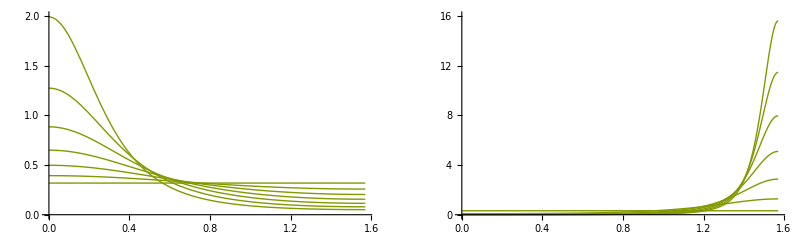

```mathematica
GraphicsRow[{Plot[trowbridgereitz/.αtr->#&/@Range[0.4,1.0,0.1],{θ,0,π/2},{PlotRange->{0,2},PlotStyle->trCol}],Plot[trowbridgereitz/.αtr->#&/@Range[1,7],{θ,0,π/2},{PlotRange->{0,16},PlotStyle->trCol}]},ImageSize->Full]
```

On the left, we see that the parameterization behaves approximately like Beckmann’s: higher is rougher. Unlike Beckmann, a value of 1.0 gives a uniform distribution (flat line). On the right, we see that the Trowbridge-Reitz distribution also supports “super-rough” distributions, like Beckmann.

Let’s compare Trowbridge-Reitz to Phong for the rough-to-moderate range (on the left) and for smoother surfaces (on the right0. We use the Beckmann parameter equivalence, since behavior with respect to the parameterization appears similar:

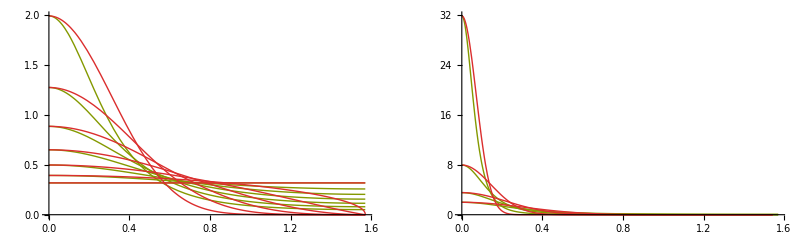

```mathematica
GraphicsRow[{Plot[{trowbridgereitz/.αtr->#&/@Range[0.4,0.9,0.1],trowbridgereitz/.αtr->1.0,phong/.αp->αb2αp[#]&/@Range[0.4,1.0,0.1]},{θ,0,π/2},PlotStyle->{trCol,{trCol,Thick},pCol}],Plot[{trowbridgereitz/.αtr->#&/@Range[0.1,0.4,0.1],phong/.αp->αb2αp[#]&/@Range[0.1,0.4,0.1]},{θ,0,π/2},PlotStyle->{trCol,pCol}]},ImageSize->Full]
```

The distributions are somewhat similar, but the Trowbridge-Reitz distribution seems to have narrower peaks and longer “tails” across the entire range (except for the uniform distribution which is identical for both).

Finally, here’s an interactive plot comparing it to Phong:

```mathematica
Manipulate[Plot[{trowbridgereitz/.αtr->a,phong/.αp->αb2αp[a]},{θ,0,π/2},PlotStyle->{trCol,pCol}],{{a,0.25},0.01,1.0}]
```

## ABC NDF

```mathematica
unnormalizedabc=1/(1+αabc1(1-Cos[θ]))^αabc2;
```

```mathematica
abcnormf=Integrate[unnormalizedabc Sin[θ]Cos[θ],{ϕ,-π,π}, {θ,0,π/2},Assumptions->{αabc1>0,αabc2>0}]
```

(2 π (1+αabc1)^-αabc2 ((1+αabc1)^2+(1+αabc1)^αabc2 (-1+αabc1 (-2+αabc2))))/(αabc1^2 (-2+αabc2) (-1+αabc2))

```mathematica
abc=unnormalizedabc/abcnormf
```

(αabc1^2 (1+αabc1)^αabc2 (-2+αabc2) (-1+αabc2) (1+αabc1 (1-Cos[θ]))^-αabc2)/(2 π ((1+αabc1)^2+(1+αabc1)^αabc2 (-1+αabc1 (-2+αabc2))))

The normalization term is somewhat complex, and it is likely that a much cheaper function could be fitted to it. In addition, the normalization factor causes this function to have (removable) singularities at αabc2 = 1.0 and αabc2 = 2.0 (another reason to fit a simpler function, which would presumably not have these removable singularities).

In the following graphs we will avoid these exact values by adding a small epsilon where needed. Since the parameter space is two-dimensional, we’ll need more plots:

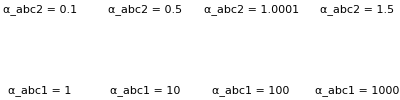

```mathematica
plot1[x_]:=Labeled[Plot[abc/.{αabc1->#,αabc2->x}&/@{1,10,100,1000},{θ,0,π/2},PlotStyle->abcCol],"α_abc2 = "<>ToString[x]]
plot2[x_]:=Labeled[Plot[abc/.{αabc1->x,αabc2->#}&/@{0.1,0.5,1.0001,1.5},{θ,0,π/2},PlotStyle->abcCol],"α_abc1 = "<>ToString[x]]
GraphicsGrid[{plot1/@{0.1,0.5,1.0001,1.5},plot2/@{1,10,100,1000}}, ImageSize->Full, AspectRatio->0.25]
```

And here’s an interactive plot:

```mathematica
Manipulate[Plot[abc/.{αabc1->a,αabc2->b},{θ,0,π/2},PlotStyle->abcCol],{a,1.0,1000.0},{b,0.25,2.5}]
```

Experimenting with various values shows us that the value of αabc2 appears to control the shape, while the value of αabc1 controls the roughness. (They are not cleanly separated, so when varying αabc2 you need to change αabc1 to keep the same roughness.) Let’s see if we can fit Trowbridge-Reitz using ABC:

```mathematica
Manipulate[Plot[{trowbridgereitz/.αtr->ktr,abc/.{αabc1->kabc1,αabc2->kabc2}},{θ,0,π/2},PlotStyle->{trCol,abcCol}],{{ktr,0.5},0.1,0.8},{{kabc1,6.3},1.04,254.0},{{kabc2,1.75},0.25,2.5}]
```

We can see that an αabc2 value of about 1.75 fits pretty well to Trowbridge-Reitz across the roughness range (less well for rough surfaces, better for smooth ones). Note that we don’t have an equivalence between them, so we just manually adjust the αabc1 parameter of the ABC curves until the peaks coincide with the Trowbridge-Reitz ones.

Now let’s try to fit Phong with ABC:

```mathematica
Manipulate[Plot[{phong/.αp->8000.0^klogphong,abc/.{αabc1-> kabc1,αabc2->1/kabc2recip}},    {θ,0,π/2},PlotStyle->{pCol,abcCol}],{{klogphong,0.5},0.0,1.0},{{kabc1,0.0905},0.0001,10.0},{{kabc2recip,0.001},0.0001,0.999}]
```

It seems that ABC asymptotically approaches Phong as the value of αabc2 approaches infinity (here we also lacked an equivalence so we adjusted αabc1 values manually until the peaks matched).

Let’s demonstrate ABC’s fit to Trowbridge-Reitz with a static plot for αabc2 = 1.75, and to Phong with a static plot for αabc2 set to a high value (1000):

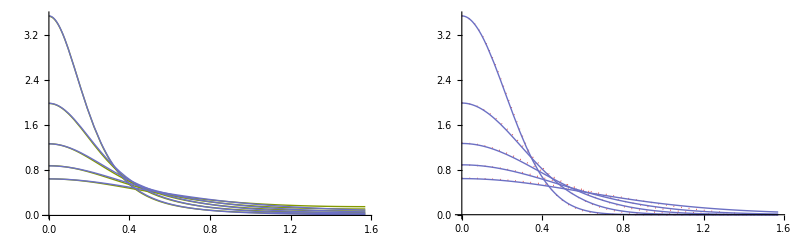

```mathematica
GraphicsRow[{Plot[{trowbridgereitz/.αtr->#&/@Range[0.3,0.7,0.1],abc/.{αabc1->#,αabc2->1.75}&/@{23.5,11.6,6.3,3.55,2.0}},{θ,0,π/2},PlotStyle->{{trCol,Thick},abcCol}],Plot[{phong/.αp->αb2αp[#]&/@Range[0.3,0.7,0.1],abc/. {αabc1-> #,αabc2-> 1000.0}&/@{0.0212,0.0114,0.0068,0.0043,0.0026}},{θ, 0,π/2},PlotStyle->{{pCol,Thick,Dotted}, abcCol}]},ImageSize->Full]
```

Since they are not directly apparent from the Plot command, let’s see the range of Phong parameters covered in the right plot:

```mathematica
αb2αp[0.3]
```

20.2222

```mathematica
αb2αp[0.7]
```

2.08163

As we have seen, with an αabc2 value of 1.75, ABC can mimic Trowbridge-Reitz quite well. With higher values, ABC can approach the appearance of Phong. (It should be noted that these are much higher than any of the values fitted to the Matusik dataset by Low et al.; this may indicate that real-world materials do not typically exhibit Gaussian normal distributions.) With αabc2 values lower than 1.75, the ABC distribution is even “spikier” than Trowbridge-Reitz; we will look at a value of 0.5 (a relatively low value for the Matusik dataset fitting performed in the paper by Low et al. – lower values were only used for very rough surfaces), comparing it to Trowbridge-Reitz (manually adjusted so the peaks match):

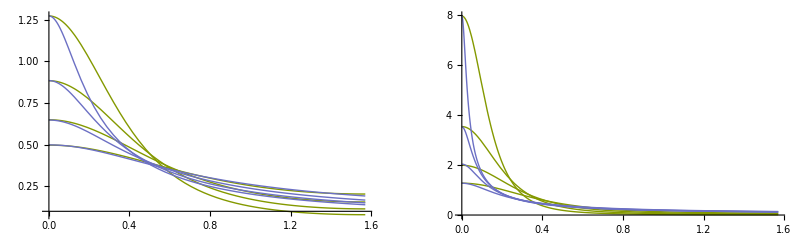

```mathematica
GraphicsRow[{Plot[{trowbridgereitz/.αtr->#&/@Range[0.5,0.8,0.1],abc/.{αabc1->#,αabc2->0.5}&/@{82.5,33.5,14.0,5.75}},{θ,0,π/2},PlotStyle->{trCol,abcCol}],Plot[{trowbridgereitz/.αtr->#&/@Range[0.2,0.5,0.1],abc/.{αabc1->#,αabc2->0.5}&/@{4250,785,240,82.5}},{θ,0,π/2},PlotStyle->{trCol,abcCol}]},ImageSize->Full]
```

We see that with an αabc2 value of 0.5, ABC is significantly “spikier” than Trowbridge-Reitz when modeling rough surfaces (on the left), and extremely so when modeling smooth ones (on the right).

## Shifted Gamma Distribution

```mathematica
p22[x_]:=αsgd1^(αsgd2-1)/Gamma[1-αsgd2,αsgd1](ⅇ^(-(αsgd1^2+x)/αsgd1))/((αsgd1^2+x)^αsgd2)
```

```mathematica
sgd=p22[(1-Cos[θ]^2)/Cos[θ]^2]/(π Cos[θ]^4)
```

(ⅇ^(-(αsgd1^2+(1-Cos[θ]^2) Sec[θ]^2)/αsgd1) αsgd1^(-1+αsgd2) Sec[θ]^4 (αsgd1^2+(1-Cos[θ]^2) Sec[θ]^2)^-αsgd2)/(π Gamma[1-αsgd2,αsgd1])

First, let’s confirm that it’s normalized, using an analytical integral:

```mathematica
sgdnormf=Integrate[sgd Sin[θ]Cos[θ],{ϕ,-π, π},{θ,0,π/2},Assumptions->{αsgd1>0,αsgd2>0}]
```

1

Yes, it’s normalized. Let’s take a look at various parameter values, spanning the rough-to-moderate part of the range of values used for fitting SGD to the Matusik database:

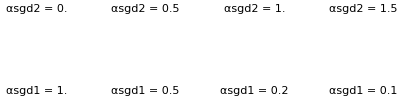

```mathematica
plot1[x_]:=Labeled[Plot[sgd/.{αsgd1->#,αsgd2->x}&/@{1.0,0.5,0.2,0.1},{θ,0,π/2},PlotStyle->sgdCol],"αsgd2 = "<>ToString[x]]
plot2[x_]:=Labeled[Plot[sgd/.{αsgd1->x,αsgd2->#}&/@{0.0,0.5,1.0,1.5},{θ,0,π/2},PlotStyle->sgdCol],"αsgd1 = "<>ToString[x]]
GraphicsGrid[{plot1/@{0.0,0.5,1.0,1.5},plot2/@{1.0,0.5,0.2,0.1}},ImageSize->Full,AspectRatio->0.25]
```

Let’s look at an interactive graph with the parameters covering the range of fitted values for the Matusik database:

```mathematica
Manipulate[Plot[sgd/.{αsgd1->a,αsgd2->b},{θ,0,π/2},PlotStyle->sgdCol],{{a,0.25},0.0001,1.0},{b,0.0,1.5}]
```

Finally, let’s compare it with ABC:

```mathematica
Manipulate[Plot[{sgd/.{αsgd1->a,αsgd2->b},abc/.{αabc1->c,αabc2->d}},{θ,0,π/2},PlotStyle->{sgdCol,abcCol}],{{a,0.25},0.0001,1.0},{b,0.0,1.5},{c,1.0,1000.0},{d,0.25,2.5}]
```